```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookAutoSave->True]
```

## Benchmark point

```mathematica
Get["cBE_routines.wl"]
```

```mathematica
(* settings *)
ξinf=0.0001 (*initial condition. Initial ratio of Tdm/Tsm*);
Ti = 150.(*Gev, initial temperature*);
xi = mphi/Ti; (*initial proxy of time*)
```

```mathematica
(* model parameters*)
mphi = 0.0000129343; (*gev*);
mchi =2.22263*10^-6;(*gev*)
lhphi =1.10727*10^-9; (*portal*);
lphi=0.000887725;
lphi0=10^-20;
κ= 0.(*8.02293*10^-9*);
```

```mathematica
xf=5.; (*Final point*)
(* run ODE *)
OPTION["Monitor"]=False;
AbsoluteTiming[sol1=cBEsolver[mphi,lphi,lhphi,ξinf,mchi,κ,xf]][[1]];//Quiet
Tϕ[x_]:=sol1[[1]][x];
Nϕ[x_]:=sol1[[2]][x];
Yϕ[x_]:=sol1[[3]][x];
```

```mathematica
AbsoluteTiming[sol0=cBEsolver[mphi,lphi0,lhphi,ξinf,mchi,κ,xf]][[1]];//Quiet
Tϕ0[x_]:=sol0[[1]][x];
Nϕ0[x_]:=sol0[[2]][x];
Yϕ0[x_]:=sol0[[3]][x];
```

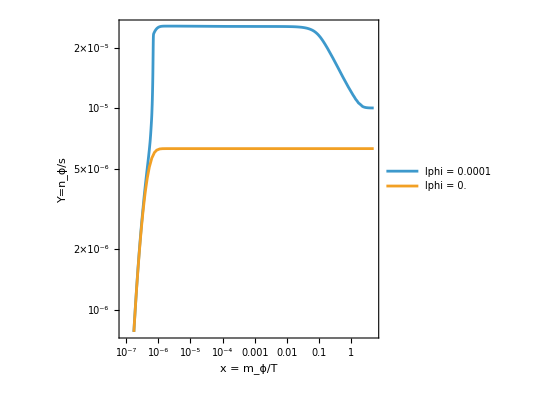

```mathematica
pY=LogLogPlot[{Yϕ[x],Yϕ0[x]},{x,xi,xf},Frame->True,FrameLabel->{"x = m_ϕ/T","Y=n_ϕ/s"},PlotLegends->{"lphi = 0.0001","lphi = 0."}, AspectRatio->1]
```

The ratio between the observed DM relic abundance and the model’s prediction (Y_ϕ(xf)/Y_obs) is the last output of the cBEsolver routine

```mathematica
Print["The ratio with self interactions is: "<>ToString[sol1[[-1]]]];
```

The ratio with self interactions is: 0.68601

```mathematica
Print["The ratio without self interactions is: "<>ToString[sol0[[-1]]]];
```

The ratio without self interactions is: 0.186699

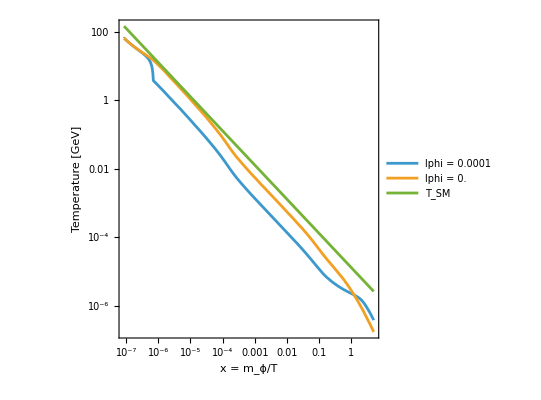

```mathematica
pY=LogLogPlot[{Tϕ[x],Tϕ0[x], mphi/x},{x,xi,xf},Frame->True,FrameLabel->{"x = m_ϕ/T","Temperature [GeV]"},PlotLegends->{"lphi = 0.0001","lphi = 0.","T_SM"}, AspectRatio->1]
```

```mathematica
rate3to2=RateCannibal3to2[Tϕ,Yϕ,lphi,mphi];
rate2to3=RateCannibal2to3[Tϕ,Yϕ,lphi,mphi];
```

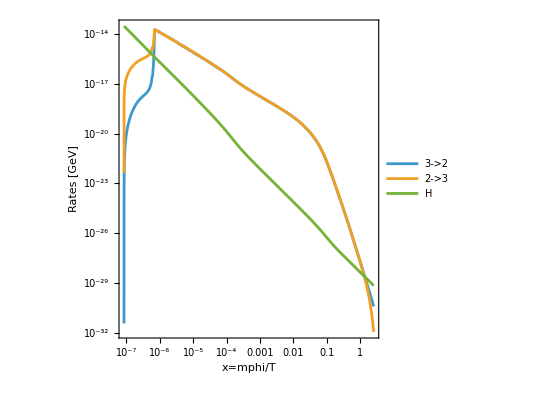

```mathematica
ratesplot=LogLogPlot[{rate3to2[x],rate2to3[x],H[mphi/x]},{x,xi,2.5},Frame->True,FrameLabel->{"x=mphi/T","Rates [GeV]"},PlotLegends->{"3->2","2->3","H"}, AspectRatio->1]
```